```mathematica
SetDirectory["/Users/rajdbz/Reservoir/Code/VonMises"]
```

/Users/rajdbz/Reservoir/Code/VonMises

```mathematica
F[x1_,x2_ ,A_,A2_,B_,B2_,lcc_, lcs_,lsc_,lss_,m1_,m2_]:=Exp[A*Cos[x1] + A2*Cos[2*x1] + B*Sin[x1] + B2*Sin[2*x1] + lcc*Cos[x1-m1]*Cos[x2-m2] + lcs*Cos[x1-m1]*Sin[x2-m2] +lsc*Sin[x1-m1]*Cos[x2-m2] +  lss*Sin[x1-m1]*Sin[x2-m2]]
```

```mathematica
Margf[x2_ ,A_,A2_,B_,B2_,lcc_, lcs_,lsc_,lss_,m1_,m2_]:=Module[{Ja,Jb,k1,mu1,k2,mu2,dmu,G0},Ja = lcc*Cos[x2-m2]*Cos[m1] +  lcs*Sin[x2-m2]*Cos[m1] -  lsc*Cos[x2-m2]*Sin[m1] -  lss*Sin[x2-m2]*Sin[m1];
Jb = lcc*Cos[x2-m2]*Sin[m1] +  lcs*Sin[x2-m2]*Sin[m1] +  lsc*Cos[x2-m2]*Cos[m1] +  lss*Sin[x2-m2]*Cos[m1];
k1 = Sqrt[(A+Ja)^2 + (B + Jb)^2 ];
mu1 = ArcTan[A+Ja,B+Jb];
k2 = Sqrt[A2^2 + B2^2];
mu2 = 0.5*ArcTan[A2,B2];
dmu = Mod[mu1 - mu2,Pi];
G0 =  BesselI[0,k1]*BesselI[0,k2];
For[n=1,n≤2,n++,G0 = G0 + 2*BesselI[2*n,k1]*BesselI[n,k2]*Cos[2*n*dmu]];
G0
]
```

```mathematica
A = 2; A2 = -3; B = 0.7; B2 = 0.8; m1 = 0.2; m2= -0.9;
lcc = 1; lcs = -2; lsc = 1.5; lss = -3;
```

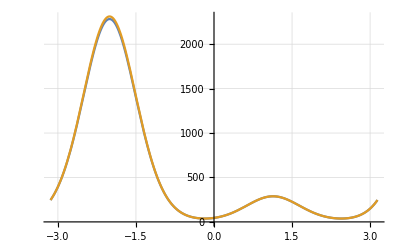

```mathematica
Plot[{NIntegrate[F[x1,x2,A,A2,B,B2,lcc,lcs,lsc,lss,m1,m2],{x1,-Pi,Pi}],2*Pi*Margf[x2,A,A2,B,B2,lcc,lcs,lsc,lss,m1,m2]},{x2,-Pi,Pi},GridLines->Automatic]
```

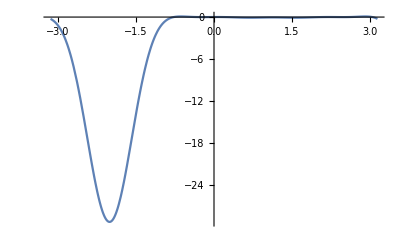

```mathematica
Plot[NIntegrate[F[x1,x2,A,A2,B,B2,lcc,lcs,lsc,lss,m1,m2],{x1,-Pi,Pi}]-2*Pi*Margf[x2,A,A2,B,B2,lcc,lcs,lsc,lss,m1,m2],{x2,-Pi,Pi}, PlotRange->All]
```

```mathematica
VonMises2D[x1_,x2_ ,k1_,k2_,m1_,m2_,lcc_, lcs_,lsc_,lss_]:=Exp[k1*Cos[(x1-m1)] + k2*Cos[(x2-m2)] + lcc*Cos[(x1-m1)]*Cos[(x2-m2)] + lcs*Cos[(x1-m1)]*Sin[(x2-m2)] +lsc*Sin[(x1-m1)]*Cos[(x2-m2)] +  lss*Sin[(x1-m1)]*Sin[(x2-m2)]]
```

```mathematica
k1 = 0.11; k2 = 0.63; m1 = -2.05; m2 = 2.49; lcc = 0.87; lcs = 0.6; lsc =0.01; lss = 1.07;
Z = NIntegrate[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss],{x1,-Pi,Pi},{x2,-Pi,Pi}]
```

57.5194

```mathematica
p1 = Plot[NIntegrate[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss]/Z,{x2,-Pi,Pi}],{x1,-Pi,Pi},PlotRange->All];
p2 = Plot[NIntegrate[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss]/Z,{x1,-Pi,Pi}],{x2,-Pi,Pi},PlotStyle->Red, PlotRange->All];
```

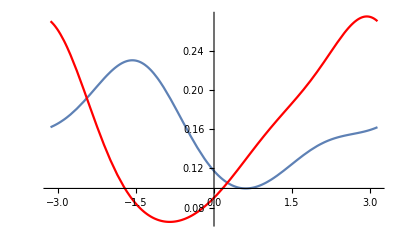

```mathematica
Show[p1,p2]
```

```mathematica
V3D[x1,x2,x3,k1_,k2_,k3_,m1_,m2_,m3_,lcc12_, lcs12_,lsc12_,lss12_,lcc23_, lcs23_,lsc23_,lss23_,lcc13_, lcs13_,lsc13_,lss13_]:=VonMises2D[x1,x2,k1,k2,m1,m2,lcc12, lcs12,lsc12,lss12]*VonMises2D[x2,x3,0,k3,0,m3,lcc23, lcs23,lsc23,lss23]*VonMises2D[x1,x3,0,0,0,0,lcc13, lcs13,lsc13,lss13]
```

```mathematica
J =Import["/Users/rajdbz/Reservoir/Code/VonMises/J.mat"];
 J = J[[1]];
```

```mathematica
AdjMat =Import["/Users/rajdbz/Reservoir/Code/VonMises/AdjMat.mat"];
 AdjMat = AdjMat[[1]];
```

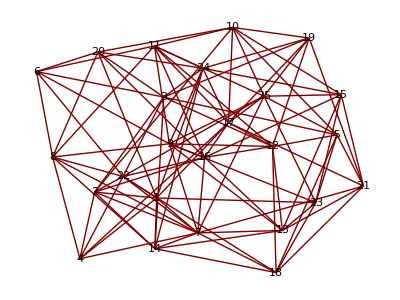

```mathematica
GraphPlot[AdjMat,VertexLabeling->True]
```

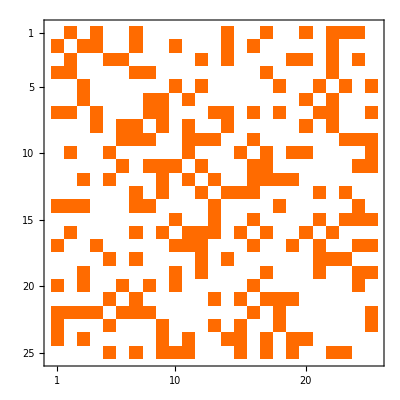

```mathematica
MatrixPlot[AdjMat]
```

```mathematica
Dimensions[J]
```

{4,25,25}

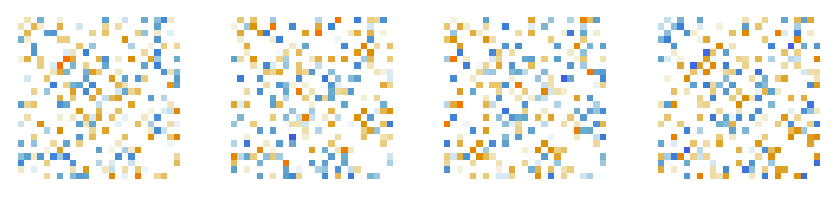

```mathematica
GraphicsRow[MatrixPlot[#,Frame->False]&/@J]
```

```mathematica
GraphPlot3D[AdjMat,VertexLabeling->True]
```

-Graphics3D-

```mathematica
Deg = Total[AdjMat]
```

{9,8,9,6,7,6,12,8,10,8,9,9,8,8,7,10,10,7,7,7,7,10,7,9,10}

```mathematica
Dimensions[J]
```

{4,25,25}

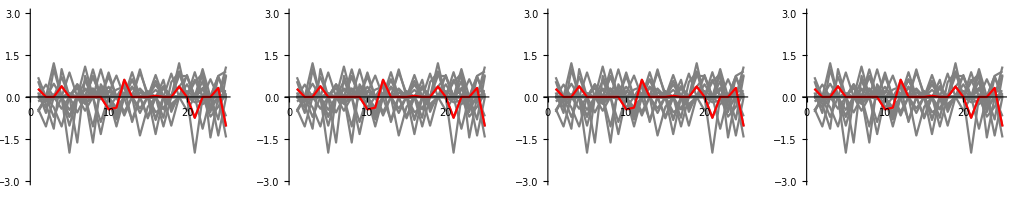

```mathematica
p11= ListLinePlot[J⟦4⟧,PlotRange->{-3,3},PlotStyle->Gray];
p12 = ListLinePlot[J⟦4,17⟧,PlotRange->{-3,3},PlotStyle->Red];
p21= ListLinePlot[J⟦4⟧,PlotRange->{-3,3},PlotStyle->Gray];
p22 = ListLinePlot[J⟦4,17⟧,PlotRange->{-3,3},PlotStyle->Red];
p31= ListLinePlot[J⟦4⟧,PlotRange->{-3,3},PlotStyle->Gray];
p32 = ListLinePlot[J⟦4,17⟧,PlotRange->{-3,3},PlotStyle->Red];
p41= ListLinePlot[J⟦4⟧,PlotRange->{-3,3},PlotStyle->Gray];
p42 = ListLinePlot[J⟦4,17⟧,PlotRange->{-3,3},PlotStyle->Red];
GraphicsRow[{Show[p11,p12],Show[p21,p22],Show[p31,p32],Show[p41,p42]}]
```